## VoronoiToTissue-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (10-Nov-2012)) loaded Sat 10 Nov 2012 15:01:22
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

```mathematica
r:= RandomReal[{0, 100}]; 
xy:= {r, r}; 
v=Table[xy, {25}]
```

{{16.7517,43.173},{10.0808,89.3778},{69.2303,47.3283},{75.3238,22.3747},{17.4395,33.6323},{21.1674,93.5355},{55.4218,83.9447},{38.4068,23.6459},{31.9079,73.1756},{31.8536,59.6376},{56.3249,82.1451},{62.4323,26.5921},{42.58,86.2306},{9.68872,24.146},{59.6176,18.8999},{67.5685,61.9854},{17.1071,80.0251},{45.4669,97.0367},{35.0931,13.5533},{90.5617,22.3955},{85.064,20.9021},{92.5348,80.8983},{27.6607,74.301},{54.4862,31.1371},{78.4341,12.277}}

```mathematica
q=VoronoiToTissue[v, {{-2, -2}, {110, -1}, {105, 107},{73, 119},  {-3, 106}}]
```

Tissue[{{3.1507,37.3974},{13.1494,61.6355},{14.4867,62.6028},{17.1543,87.3762},{23.2703,20.9587},{24.9818,22.4635},{26.414,84.5934},{27.8459,66.4228},{30.5449,85.9879},{32.4115,83.6535},{33.1237,39.5581},{33.4359,94.4622},{34.9775,41.614},{39.4417,42.4268},{45.9934,72.5507},{47.6158,15.032},{47.9274,79.0573},{48.2745,66.3409},{49.1046,21.686},{49.4302,65.0844},{49.5424,50.4478},{49.8873,90.0671},{50.2509,52.5992},{56.0093,24.5813},{63.5227,37.717},{67.5309,20.3654},{68.7568,14.8241},{72.2693,34.8496},{74.3423,78.9786},{74.8095,92.5477},{76.2514,110.114},{79.6719,18.1862},{82.5717,37.3654},{83.4075,37.8662},{90.8395,57.2011},{91.1502,9.36305},{99.2126,51.3884},{110,-1},{105,107},{73,119},{-3,106},{-2,-2},{107.588,51.1059},{78.5807,116.907},{30.937,111.805},{9.37609,108.117},{-2.68952,72.4683},{-2.59062,61.7873},{-2.38381,39.4518},{13.7561,-1.85932},{51.2254,-1.52477},{63.0395,-1.41929},{99.8719,-1.09043}},{{1,5},{1,11},{1,49},{2,3},{2,13},{2,48},{3,7},{3,8},{4,7},{4,46},{4,47},{5,6},{5,50},{6,11},{6,16},{7,9},{8,10},{8,18},{9,10},{9,12},{10,15},{11,13},{12,22},{12,45},{13,14},{14,19},{14,21},{15,17},{15,18},{16,19},{16,51},{17,22},{17,30},{18,20},{19,24},{20,23},{20,29},{21,23},{21,25},{22,31},{23,35},{24,25},{24,26},{25,28},{26,27},{26,28},{27,32},{27,52},{28,33},{29,30},{29,35},{30,31},{31,44},{32,33},{32,36},{33,34},{34,36},{34,37},{35,37},{36,53},{37,43},{38,43},{38,53},{39,43},{39,44},{40,44},{40,45},{41,46},{41,47},{42,49},{42,50},{45,46},{47,48},{48,49},{50,51},{51,52},{52,53}},{{74,3,2,22,5,6},{69,11,10,68},{38,39,44,49,56,58,59,41},{45,47,54,49,46},{1,12,14,2},{72,10,9,16,20,24},{32,33,52,40},{22,14,15,30,26,25},{18,29,21,17},{4,5,25,27,38,36,34,18,8},{28,29,34,37,50,33},{43,46,44,42},{19,21,28,32,23,20},{71,13,1,3,70},{76,48,45,43,35,30,31},{36,41,51,37},{73,6,4,7,9,11},{67,24,23,40,53,66},{75,31,15,12,13},{61,58,57,60,63,62},{54,55,57,56},{65,53,52,50,51,59,61,64},{7,8,17,19,16},{26,35,42,39,27},{77,60,55,47,48}}]

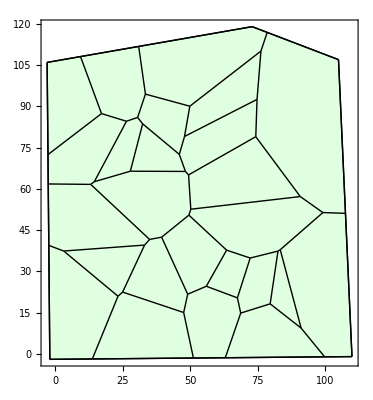

```mathematica
ShowTissue[q, Frame->True]
```